3а.Разложить в ряд Фурье по синусам, продолжив нечётно функцию.

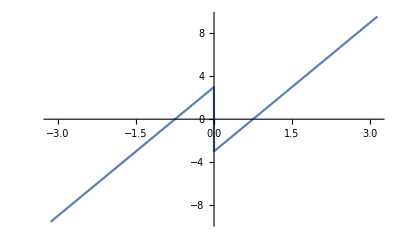

{{(-12+8 π)/π,4.18028},{(-12-2 (-6+8 π))/(4 π),-4.},{(-18+3 (-6+8 π))/(9 π),1.39343},{(-24-4 (-6+8 π))/(16 π),-2.},{(-30+5 (-6+8 π))/(25 π),0.836056},{(-36-6 (-6+8 π))/(36 π),-1.33333},{(-42+7 (-6+8 π))/(49 π),0.597183},{(-48-8 (-6+8 π))/(64 π),-1.},{(-54+9 (-6+8 π))/(81 π),0.464476},{(-60-10 (-6+8 π))/(100 π),-0.8}}

(-12+8 π)/π | 4.18028
(-12-2 (-6+8 π))/(4 π) | -4.
(-18+3 (-6+8 π))/(9 π) | 1.39343
(-24-4 (-6+8 π))/(16 π) | -2.
(-30+5 (-6+8 π))/(25 π) | 0.836056
(-36-6 (-6+8 π))/(36 π) | -1.33333
(-42+7 (-6+8 π))/(49 π) | 0.597183
(-48-8 (-6+8 π))/(64 π) | -1.
(-54+9 (-6+8 π))/(81 π) | 0.464476
(-60-10 (-6+8 π))/(100 π) | -0.8

((-12+8 π) Sin[t])/π+((-12-2 (-6+8 π)) Sin[2 t])/(4 π)

((-12+8 π) Sin[t])/π+((-12-2 (-6+8 π)) Sin[2 t])/(4 π)+((-18+3 (-6+8 π)) Sin[3 t])/(9 π)+((-24-4 (-6+8 π)) Sin[4 t])/(16 π)

((-12+8 π) Sin[t])/π+((-12-2 (-6+8 π)) Sin[2 t])/(4 π)+((-18+3 (-6+8 π)) Sin[3 t])/(9 π)+((-24-4 (-6+8 π)) Sin[4 t])/(16 π)+((-30+5 (-6+8 π)) Sin[5 t])/(25 π)+((-36-6 (-6+8 π)) Sin[6 t])/(36 π)+((-42+7 (-6+8 π)) Sin[7 t])/(49 π)+((-48-8 (-6+8 π)) Sin[8 t])/(64 π)

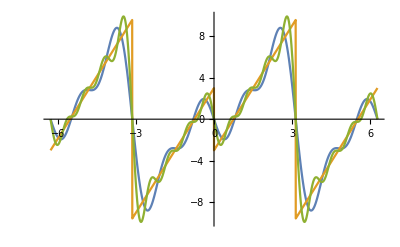

3 б) Разложить в ряд Фурье по косинусам, продолжив чётно функцию.

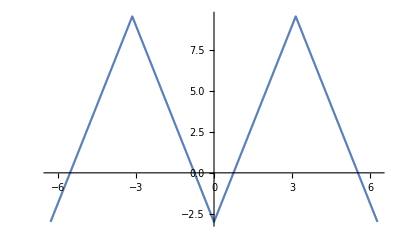

3.28319-(16 Cos[t])/π

3.28319-(16 Cos[t])/π-(16 Cos[3 t])/(9 π)

3.28319-(16 Cos[t])/π-(16 Cos[3 t])/(9 π)-(16 Cos[5 t])/(25 π)-(16 Cos[7 t])/(49 π)

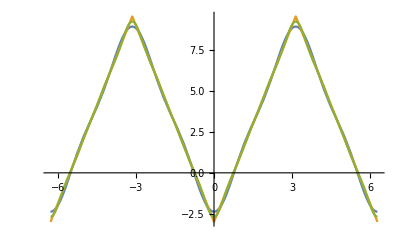

```mathematica
Clear[f]
Text["3а.Разложить в ряд Фурье по синусам, продолжив нечётно функцию.  "]
f[t_]:=4*t-3/;0≤t≤Pi
f[t_]:=-f[-t]/;-Pi≤t<0
f[t_]:=f[t-2*Pi]/;t≥Pi
f[t_]:=f[t+2*Pi]/;t≤-Pi

Plot[f[t],{t,-Pi,Pi}]
Clear[a,b,fs,L,ex,a1,b1,fourier]
L=Pi;
b[k_]:=2/L*N[Integrate[f[t]*Sin[k*t],{t,0,L}]]
b1[k_]:=(-6*k+8*Sin[k*Pi]-(8*Pi-6)*k*Cos[k*Pi])/(Pi*k^2)
coeffs = Table[{b1[i],b[i]},{i,1,10}]
TableForm[coeffs]
row[n_,t_]:=Sum[b1[k]*Sin[k*t],{k,1,n}];
row[2,t]
row[4,t]
row[8,t]
Plot[{row[4,t],f[t],row[8,t]},{t,-2*Pi,2*Pi}]
Text["3 б) Разложить в ряд Фурье по косинусам, продолжив чётно функцию.  "]
Clear[f,a,row,coeffs,L]
f[t_]:=4*t-3/;0≤t≤Pi
f[t_]:=f[-t]/;-Pi≤t<0
f[t_]:=f[t-2*Pi]/;t≥Pi
f[t_]:=f[t+2*Pi]/;t≤-Pi
Plot[f[t],{t,-2*Pi,2*Pi}]
L=Pi;
a[0]:=2/L*NIntegrate[f[t],{t,0,L}]
a[k_]:=2/L*N[Integrate[f[t]*Cos[k*t],{t,0,L}]]
a1[k_]:=((8*Pi-6)*k*Sin[k*Pi]+8*Cos[k*Pi]-8)/(Pi*k^2)
row[n_,t_]:=a[0]/2+Sum[a1[k]*Cos[k*t],{k,1,n}];
row[2,t]
row[4,t]
row[8,t]
Plot[{row[4,t],f[t],row[8,t]},{t,-2*Pi,2*Pi}]
```